#### Метод Рунге - Кутты для решения задачи Коши для однородного дифференциального уравнения 1 - го порядка

```mathematica
(*http://mathprofi.ru/metody_eilera_i_runge_kutty.html*)
```

Euler Method

```mathematica
a = -2;
y'[x_,y_]:= a * y - x^2;
Subscript[y, 0]=1;
Subscript[x, 0]=0;
z'[x_,z_]:=-z-a*x;

h=0.1;
Subscript[x, 0]=0;
Do[Subscript[x, i]=Subscript[x, i-1]+h,{i,1,10}];
```

```mathematica
Do[Subscript[y, i]=Subscript[y, i-1]+h*y'[Subscript[x, i-1],Subscript[y, i-1]],{i,1,10}];
```

```mathematica
(*Разворачиваем координаты (0.5, 0.4, 0.3, 0.2, 0.1, 0.0)*)
Subscript[z, 0]=Subscript[y, 5];
Do[Subscript[x, i]=0.5-i*h,{i,0,5}]
(*For[i=5,i>0,i--,Subscript[z, i-1]=Subscript[z, i]+h*z'[Subscript[x, i],Subscript[z, i]];];*)
Do[Subscript[z, i]=Subscript[z, i-1]-h*z'[Subscript[x, i-1],Subscript[z, i-1]],{i,1,5}];
(*Разворачиваем обратно*)
Do[Subscript[f, i]=Subscript[z, 5-i],{i,0,5}];
```

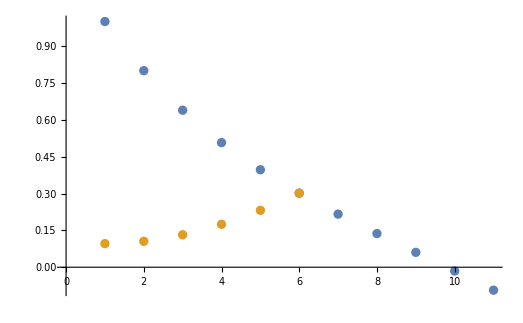

0.0959306

```mathematica
ListPlot[{Table[Subscript[y, i],{i,0,10}],Table[Subscript[f, i],{i,0,5}]}]
Print[Subscript[f, 0]]
```

Euler Cachy Method

```mathematica
Do[Unset[Subscript[y, i]],{i,0,10}]
Do[Unset[Subscript[z, i]],{i,0,5}]
a = -2;
y'[x_,y_]:= a * y - x^2;
Subscript[y, 0]=1;
Subscript[ỹ, 0]=Subscript[y, 0];
Subscript[x, 0]=0;
Do[Subscript[x, i]=Subscript[x, i-1]+h,{i,1,10}];
z'[x_,z_]:=-z+-a*x;
(*Subscript[z, 0]=α;*)
Subscript[z̃, 0]=Subscript[z, 0];
h=0.1;
```

```mathematica
For[i=1,i≤10,i++,
Subscript[ỹ, i]=Subscript[y, i-1]+h*y'[Subscript[x, i-1],Subscript[y, i-1]];
Subscript[y, i]=Subscript[y, i-1]+0.5*h(y'[Subscript[x, i-1],Subscript[y, i-1]] + y'[Subscript[x, i],Subscript[ỹ, i]]);
];
```

```mathematica
Subscript[z, 5]=Subscript[y, 5];
Subscript[z̃, 5]=Subscript[z, 5];
For[i=5,i>0,i--,
Subscript[z̃, i-1]=Subscript[z, i]-h*z'[Subscript[x, i],Subscript[z, i]];
Subscript[z, i-1]=Subscript[z, i]-0.5*h(z'[Subscript[x, i],Subscript[z, i]] + z'[Subscript[x, i-1],Subscript[z̃, i-1]]);
];
```

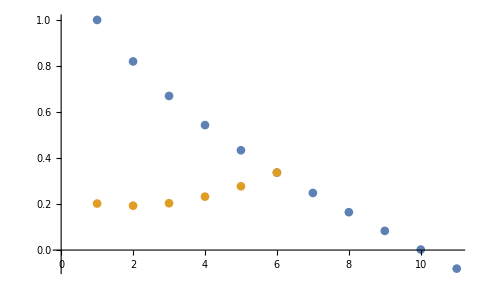

0.202104

```mathematica
ListPlot[{Table[Subscript[y, i],{i,0,10}],Table[Subscript[z, i],{i,0,5}]}]
Print[Subscript[z, 0]]
```

Traditional Runge Kutta Method

```mathematica
Do[Unset[Subscript[y, i]],{i,0,10}]
Do[Unset[Subscript[z, i]],{i,0,5}]
a = -2;
y'[x_,y_]:= a * y - x^2;
Subscript[y, 0]=1;
Subscript[x, 0]=0;
Do[Subscript[x, i]=Subscript[x, i-1]+h,{i,1,10}];
z'[x_,z_]:=-z-a*x;
h=0.1;
koff=h/6;
```

```mathematica
For[i=1,i≤10,i++,
Subscript[k, 1]=y'[Subscript[x, i-1],Subscript[y, i-1]];
Subscript[k, 2]=y'[Subscript[x, i-1]+0.5*h,Subscript[y, i-1]+0.5*h*Subscript[k, 1]];
Subscript[k, 3]=y'[Subscript[x, i-1]+0.5*h,Subscript[y, i-1]+0.5*h*Subscript[k, 2]];
Subscript[k, 4]=y'[Subscript[x, i-1]+h,Subscript[y, i-1]+h*Subscript[k, 3]];
Subscript[y, i]=Subscript[y, i-1]+koff*(Subscript[k, 1]+2*Subscript[k, 2]+2*Subscript[k, 3]+Subscript[k, 4]);
];
```

```mathematica
Subscript[z, 0]=Subscript[y, 5];
Do[Subscript[x, i]=0.5-i*h,{i,0,5}];
h = -0.1;
koff = h/6;
For[i=1,i≤5,i++,
Subscript[k, 1]=z'[Subscript[x, i-1],Subscript[z, i-1]];
Subscript[k, 2]=z'[Subscript[x, i-1]+0.5*h,Subscript[z, i-1]+0.5*h*Subscript[k, 1]];
Subscript[k, 3]=z'[Subscript[x, i-1]+0.5*h,Subscript[z, i-1]+0.5*h*Subscript[k, 2]];
Subscript[k, 4]=z'[Subscript[x, i-1]+h,Subscript[z, i-1]+h*Subscript[k, 3]];
Subscript[z, i]=Subscript[z, i-1]+koff*(Subscript[k, 1]+2*Subscript[k, 2]+2*Subscript[k, 3]+Subscript[k, 4]);
];
Do[Subscript[f, i]=Subscript[z, 5-i],{i,0,5}];
```

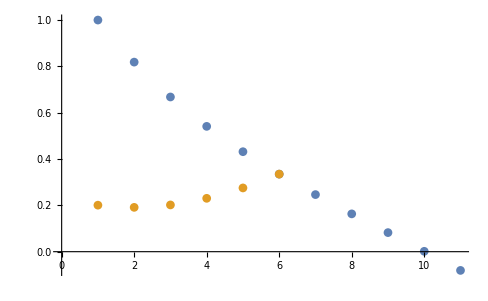

0.200801

```mathematica
ListPlot[{Table[Subscript[y, i],{i,0,10}],Table[Subscript[f, i],{i,0,10}]}]
Print[Subscript[f, 0]]
```